# Dinâmica de um vórtice - Modos Coletivos e Expansão

## Cálculo variacional das Equações de Movimento.

Segundo já calculado anteriormente, havia um problema na fase de nosso Ansatz. Como foi calculado no arquivo “Engenharia de fase”, é preciso adicionar um novo termo para a fase, dessa maneira nosso novo Ansatz é:
ψ(ρ,ϕ,z,t)=A ⅇ^(ⅈ ϕ)√(1-[(ξ(t))/ρ^2]^2-[ρ/(R_ρ(t))]^2-[z/(R_z(t))]^2)Exp{ⅈ[B(t)ρ^2+C(t)ρ^-2]/2},
Válida no intervalo de 1-[(ξ(t))/ρ^2]^2-[ρ/(R_ρ(t))]^2-[z/(R_z(t))]^2≥0.

```mathematica
FullSimplify[Solve[1-α^2/ρ^2-ρ^2-z^2==0,z]]
```

{{z→-(√(-α^2+ρ^2-ρ^4))/ρ},{z→(√(-α^2+ρ^2-ρ^4))/ρ}}

```mathematica
FullSimplify[Solve[((-α^2+ρ^2-ρ^4)^(3/2))/ρ^2==0,ρ]]
```

{{ρ→-(√(1-√(1-4 α^2)))/(√2)},{ρ→(√(1-√(1-4 α^2)))/(√2)},{ρ→-(√(1+√(1-4 α^2)))/(√2)},{ρ→(√(1+√(1-4 α^2)))/(√2)}}

```mathematica
ExpandAll[((-α^2+ρ^2-ρ^4)^(3/2))/ρ^2]
```

√(-α^2+ρ^2-ρ^4)-(α^2 √(-α^2+ρ^2-ρ^4))/ρ^2-ρ^2 √(-α^2+ρ^2-ρ^4)

```mathematica
Integrate[(8π(-α^2+ρ^2-ρ^4)^(3/2))/(3 ρ^2),ρ]
```

(2 π (-4 √(1/(-1+√(1-4 α^2))) (5 α^4+α^2 ρ^2 (-3+4 ρ^2)-ρ^4 (2-3 ρ^2+ρ^4))+ⅈ √2 (1+12 α^2) (1+√(1-4 α^2)) ρ √((1+√(1-4 α^2)-2 ρ^2)/(1+√(1-4 α^2))) √((-1+√(1-4 α^2)+2 ρ^2)/(-1+√(1-4 α^2))) EllipticE[ⅈ ArcSinh[√2 √(1/(-1+√(1-4 α^2))) ρ],(1-√(1-4 α^2))/(1+√(1-4 α^2))]-ⅈ √2 (1+√(1-4 α^2)+4 α^2 (-1+3 √(1-4 α^2))) ρ √((1+√(1-4 α^2)-2 ρ^2)/(1+√(1-4 α^2))) √((-1+√(1-4 α^2)+2 ρ^2)/(-1+√(1-4 α^2))) EllipticF[ⅈ ArcSinh[√2 √(1/(-1+√(1-4 α^2))) ρ],(1-√(1-4 α^2))/(1+√(1-4 α^2))]))/(15 √(1/(-1+√(1-4 α^2))) ρ √(-α^2+ρ^2-ρ^4))

```mathematica
∫_(√(1/2-1/2 √(1-4 α^2)))^(√(1/2+1/2 √(1-4 α^2))) (FullSimplify[∫_(-(√(-α^2+ρ^2-ρ^4))/ρ)^((√(-α^2+ρ^2-ρ^4))/ρ) (∫_0^(2π) (1-α^2/ρ^2-ρ^2-z^2)ⅆϕ)ⅆz])ρⅆρ
```

$Aborted

Por encontrar problemas ao integrar o Ansatz acima, vamos pega outro similar.
Válido no intervalo de 1-[ρ/(R_ρ(t))]^2-[z/(R_z(t))]^2≥0.

ψ(ρ,ϕ,z,t)=A (ⅇ^(ⅈ ℓ ϕ)(ρ^2/(ρ^2+(ξ(t))^2)))^(1/2)√(1-[ρ/(R_ρ(t))]^2-[z/(R_z(t))]^2)Exp{ⅈ B_ρ(t)ρ^2/2+ⅈ C(t)ρ^4/4+ⅈ B_z(t)z^2/2}
Normalizando.

```mathematica
R^2 Z Integrate[A^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]==Ν
```

R^2 Z If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,8/45 A^2 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]),Integrate[4 A^2 r^2 π-4 A^2 r^4 π-(4 A^2 r π α^2 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2))+(4 A^2 r^3 π α^2 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]==Ν

```mathematica
Series[Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)],{α,0,6}]
Expand[Series[-4ArcCoth[√(1+α^2)],{α,0,6}]]
```

(-Log[16]+4 Log[α])-α^2+(3 α^4)/8-(5 α^6)/24+O[α]^7

4 ⅈ π Floor[(π-2 Arg[α]-Arg[(-1+√(1+α^2))/(α^2 √(1+α^2))])/(2 π)]+(-4 (Log[2]-Log[α])-α^2+(3 α^4)/8-(5 α^6)/24+O[α]^7)

Onde ξ=R_ρ α.
A=√(N/(π R_ρ^2 R_z A_0)), com A_0=8/45[3+20 α^2+15 α^4-15(α^2(1+α^2))^(3/2)ArcCoth(√(1+α^2))]
ArcCoth(√(1+α^2))=-1/4Log[(1-√(1+α^2))^2/(1+√(1+α^2))^2]
Calculando os termos da Lagrangiana.
Parte “temporal”.

```mathematica
(ⅈ ℏ)/2 FullSimplify[A[t](ρ^2/(ρ^2+α[t]^2))^(1/2)Exp[-ⅈ (ϕ+Br[t]ρ^2/2+c[t]ρ^4/4+Bz[t]z^2/2)]D[A[t](ρ^2/(ρ^2+α[t]^2))^(1/2)Exp[ⅈ (ϕ+Br[t]ρ^2/2+c[t]ρ^4/4+Bz[t]z^2/2)],t]-A[t](ρ^2/(ρ^2+α[t]^2))^(1/2)Exp[ⅈ (ϕ+Br[t]ρ^2/2+c[t]ρ^4/4+Bz[t]z^2/2)]D[A[t](ρ^2/(ρ^2+α[t]^2))^(1/2)Exp[-ⅈ (ϕ+Br[t]ρ^2/2+c[t]ρ^4/4+Bz[t]z^2/2)],t]]
```

-(ℏ A[t]^2  (2 ρ^4 Br'[t]+2 z^2 ρ^2 Bz'[t]+ρ^6 c'[t]))/(4 (ρ^2+α[t]^2))

```mathematica
R^2 Integrate[((r^4 Sin[θ]^4)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
Z^2 Integrate[((r^2 Sin[θ]^2 r^2 Cos[θ]^2)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
R^4 Integrate[((r^6 Sin[θ]^6)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

ConditionalExpression[8/315 π R^2 (6-7 α^2 (3+20 α^2+15 α^4)+105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

ConditionalExpression[(8 π Z^2 (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575,α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

ConditionalExpression[8/945 π R^4 (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

L_time=-(N ℏ)/2(D_1 OverDot[B_ρ]R_ρ^2+D_2 OverDot[B_z]R_z^2+1/2 D_3 Ċ R_ρ^4)
D_1=A_1/A_0, D_2=A_2/A_0 e D_3=A_3/A_0.
A_1=8/315[6-7α^2(3+20 α^2+15 α^4)+105(α^4(1+α^2))^(3/2)ArcCoth(√(1+α^2))]
A_2=8/1575[15+7α^2(23+35 α^2+15 α^4)-105(α^2(1+α^2))^(3/2)ArcCoth(√(1+α^2))]
A_3=8/945[8-18 α^2+63 α^4+420 α^6+315 α^8-315(α^6(1+α^2))^(3/2)ArcCoth[√(1+α^2)]]
Parte cinética.

```mathematica
Collect[Collect[Expand[FullSimplify[D[(ρ^2/(ρ^2+α^2))^(1/2)Exp[ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],ρ]D[(ρ^2/(ρ^2+α^2))^(1/2)Exp[-ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],ρ]]],Br],c]
Collect[Collect[Expand[FullSimplify[D[Exp[ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],ρ]D[Exp[-ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],ρ]]],Br],c]

1/ρ^2 D[(ρ^2/(ρ^2+α^2))^(1/2)Exp[ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],ϕ]D[(ρ^2/(ρ^2+α^2))^(1/2)Exp[-ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],ϕ]

D[(ρ^2/(ρ^2+α^2))^(1/2)Exp[ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],z]D[(ρ^2/(ρ^2+α^2))^(1/2)Exp[-ⅈ(ℓ ϕ+Br ρ^2/2+Bz z^2/2+c ρ^4/4)],z]
```

α^4/((α^2+ρ^2)^3)+Br^2 ((α^4 ρ^4)/((α^2+ρ^2)^3)+(2 α^2 ρ^6)/((α^2+ρ^2)^3)+ρ^8/((α^2+ρ^2)^3))+c ((2 Br α^4 ρ^6)/((α^2+ρ^2)^3)+(4 Br α^2 ρ^8)/((α^2+ρ^2)^3)+(2 Br ρ^10)/((α^2+ρ^2)^3))+c^2 ((α^4 ρ^8)/((α^2+ρ^2)^3)+(2 α^2 ρ^10)/((α^2+ρ^2)^3)+ρ^12/((α^2+ρ^2)^3))

Br^2 ρ^2+2 Br c ρ^4+c^2 ρ^6

ℓ^2/(α^2+ρ^2)

(Bz^2 z^2 ρ^2)/(α^2+ρ^2)

```mathematica
Br^2 R^2 Integrate[((r^4 Sin[θ]^4)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
Bz^2 Z^2 Integrate[((r^2 Sin[θ]^2 r^2 Cos[θ]^2)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]

(Br c R^4)Integrate[((r^6 Sin[θ]^6)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]

R^-2 Integrate[(α^4/((r^2 Sin[θ]^2+α^2)^3))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
R^-2 Integrate[(1/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]

c^2 R^6 Integrate[((r^8 Sin[θ]^8)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

Br^2 R^2 If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]),Integrate[(8 r^4 π)/3-(8 r^6 π)/3-4 r^2 π α^2+4 r^4 π α^2+(4 r π α^4 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2))-(4 r^3 π α^4 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

-4/3 Bz^2 π Z^2 If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,-2/525 (15+161 α^2+245 α^4+105 α^6-105 α^2 (1+α^2)^(5/2) ArcTanh[1/(√(1+α^2))]),Integrate[r (-1+r^2) (r^3+3 r α^2-3 α^2 √(r^2+α^2) ArcTanh[r/(√(r^2+α^2))]),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

Br c R^4 If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]),Integrate[(32 r^6 π)/15-(32 r^8 π)/15-8/3 r^4 π α^2+8/3 r^6 π α^2+4 r^2 π α^4-4 r^4 π α^4-(4 r π α^6 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2))+(4 r^3 π α^6 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

-1/(2 R^2)π If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,-4/3+2 α^2-(2 α^4 ArcTanh[1/(√(1+α^2))])/(√(1+α^2)),Integrate[(r (-1+r^2) (r √(r^2+α^2) (2 r^2+5 α^2)+3 α^4 ArcTanh[r/(√(r^2+α^2))]))/((r^2+α^2)^(5/2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

1/R^2 If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]),Integrate[(4 r π ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2))-(4 r^3 π ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

c^2 R^6 If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,-(8 π (-48+88 α^2-198 α^4+693 α^6+4620 α^8+3465 α^10-3465 α^8 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))/10395,Integrate[(64 r^8 π)/35-(64 r^10 π)/35-32/15 r^6 π α^2+32/15 r^8 π α^2+8/3 r^4 π α^4-8/3 r^6 π α^4-4 r^2 π α^6+4 r^4 π α^6+(4 r π α^8 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2))-(4 r^3 π α^8 ArcTanh[r/(√(r^2+α^2))])/(√(r^2+α^2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

L_kin=-(N ℏ^2)/(2m)[D_1 B_ρ^2 R_ρ^2+D_2 B_z^2 R_z^2+2 D_3 B_ρ C R_ρ^4 +(D_4 ℓ^2+D_5)R_ρ^-2+D_6 C^2 R_ρ^6]
D_4=A_4/A_0 e D_5=A_5/A_0.
A_4=-8/9[4+3 α^2-3(1+α^2)^(3/2)ArcCoth(√(1+α^2))]
A_5=[2/3-α^2+(α^4(1+α^2))^(-1/2)ArcCoth(√(1+α^2))]
A_6=8/10395[48-11α^2(8-18 α^2+63 α^4+420 α^6+315 α^8)+3465(α^8(1+α^2))^(3/2)ArcCoth(√(1+α^2))]
Parte do trap.
L_trap=-N/2m ω_ρ^2[D_1 R_ρ^2+λ^2 D_2 R_z^2]
Parte do potencial de interação.

```mathematica
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

2 π If[Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0,(8 (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)),Integrate[(r (-1+r^2)^2 (r √(r^2+α^2) (2 r^2+3 α^2)-α^2 (4 r^2+3 α^2) ArcTanh[r/(√(r^2+α^2))]))/((r^2+α^2)^(3/2)),{r,0,1},Assumptions→!(Im[α]≥1||1+Im[α]≤0||α∈Reals||Re[α]≠0)]]

L_int=-(N^2 U_0 D_7)/(2π R_ρ^2 R_z)
D_7=A_7/A_0^2
A_7=16/1575[30+749 α^2+1680 α^4+945 α^6-105α^2(4+9 α^2)(1+α^2)^(3/2)ArcCoth(√(1+α^2))]
L=L_time+L_kin+L_trap+L_int
Reescalando R_ρ=a_osc r_ρ, R_z=a_osc r_z, B_ρ=a_osc^-2 β_ρ, B_z=a_osc^-2 β_z, C=a_osc^-4 ζ e τ=ω_ρ t; onde a_osc=√(ℏ/(m ω_ρ)) e γ=(N a_s)/a_osc.
L=-1/2N ℏ ω_ρ[D_1 r_ρ^2(OverDot[β_ρ]+β_ρ^2+1)+D_2 r_z^2(OverDot[β_z]+β_z^2+λ^2)+D_3 r_ρ^4(1/2 ζ̇+2 β_ρ ζ)+r_ρ^-2(D_4 ℓ^2+D_5)+D_6 ζ^2 r_ρ^6+D_7(4γ)/(r_ρ^2 r_z)]

```mathematica
eq1=Subscript[β, ρ]==D[Subscript[r, ρ][t],t]/(Subscript[r, ρ][t])+(Subscript[D1, α] D[α[t],t])/(2D1)-(D3 (Subscript[r, ρ][t])^2 ζ)/D1;
eq2=Subscript[β, z]==D[Subscript[r, z][t],t]/(Subscript[r, z][t])+(Subscript[D2, α] D[α[t],t])/(2D2);
eq3=ζ==(D3 D[Subscript[r, ρ][t],t])/(D5 (Subscript[r, ρ][t])^3)+(Subscript[D3, α] D[α[t],t])/(4D5 (Subscript[r, ρ][t])^2)-(D3 Subscript[β, ρ])/(D5 (Subscript[r, ρ][t])^2);
FullSimplify[ExpandAll[Solve[{eq1,eq2,eq3},{Subscript[β, ρ],Subscript[β, z],ζ}]]]
ClearAll[eq1,eq2,eq3]
```

{{β_ρ→((-2 D5 D1_α+D3 D3_α) α'[t])/(4 (D3^2-D1 D5))+r_ρ'[t]/r_ρ[t],β_z→(D2_α α'[t])/(2 D2)+r_z'[t]/r_z[t],ζ→((2 D3 D1_α-D1 D3_α) α'[t])/(4 (D3^2-D1 D5) r_ρ[t]^2)}}

β_ρ=OverDot[r_ρ]/r_ρ+F_1 α̇
β_z=OverDot[r_z]/r_z+F_2 α̇
ζ=F_3 α̇ r_ρ^-2
F_1=(D_3 D_3'-2 D_1' D_6)/(4(D_3^2-D_1 D_6))
F_2=D_2'/(2 D_2)
F_3=(2 D_1' D_3-D_1 D_3')/(4(D_3^2-D_1 D_6))
OverDot[β_ρ]+β_ρ^2=r_ρ^(..)/r_ρ+F_1 α^(..)+(F_1^2+F_1')(α̇)^2+2 F_1 r_ρ^-1 OverDot[r_ρ]α̇
OverDot[β_z]+β_z^2=r_z^(..)/r_z+F_2 α^(..)+(F_2^2+F_2')(α̇)^2+2 F_2 r_z^-1 OverDot[r_z]α̇
ζ^2=F_3^2(α̇)^2 r_ρ^-4
1/2 ζ̇=(F_3 α^(..))/(2 r_ρ^2)+(F_3'(α̇)^2)/(2 r_ρ^2)-F_3(α̇ OverDot[r_ρ])/r_ρ^3
2 β_ρ ζ=2 F_1 F_3(α̇)^2/r_ρ^2+2 F_3(OverDot[r_ρ]α̇)/r_ρ^3
Partes das equações de movimento.
r_ρ(OverDot[β_ρ]+β_ρ^2)=r_ρ^(..)+F_1 r_ρ α^(..)+(F_1^2+F_1')r_ρ(α̇)^2+2 F_1 OverDot[r_ρ]α̇
r_ρ^2(OverDot[β_ρ]+β_ρ^2)=r_ρ r_ρ^(..)+F_1 r_ρ^2 α^(..)+(F_1^2+F_1')r_ρ^2(α̇)^2+2 F_1 r_ρ OverDot[r_ρ]α̇
r_z(OverDot[β_z]+β_z^2)=r_z^(..)+F_2 r_z α^(..)+(F_2^2+F_2')r_z(α̇)^2+2 F_2 OverDot[r_z]α̇
r_z^2(OverDot[β_z]+β_z^2)=r_z r_z^(..)+F_2 r_z^2 α^(..)+(F_2^2+F_2')r_z^2(α̇)^2+2 F_2 r_z OverDot[r_z]α̇
ζ^2 r_ρ^5=F_3^2(α̇)^2 r_ρ
ζ^2 r_ρ^6=F_3^2(α̇)^2 r_ρ^2
r_ρ^3(ζ̇+4 β_ρ ζ)=F_3 r_ρ α^(..)+(F_3'+4 F_1 F_3)r_ρ(α̇)^2+2 F_3 OverDot[r_ρ]α̇
r_ρ^4(1/2 ζ̇+2 β_ρ ζ)=F_3/2 r_ρ^2 α^(..)+(F_3'/2+2 F_1 F_3)r_ρ^2(α̇)^2+F_3 r_ρ OverDot[r_ρ]α̇
Equações de movimento:
---------------------------------------------------------------------------------------------------
D_1(r_ρ^(..)+r_ρ)+G_1 r_ρ α^(..)+G_2 r_ρ(α̇)^2+G_3 OverDot[r_ρ]α̇-G_4 r_ρ^-3-(4γ D_7)/(r_ρ^3 r_z)=0

G_1=D_1 F_1+D_3 F_3
G_2=D_1(F_1^2+F_1')+D_3(F_3'+4 F_1 F_3)+3 D_6 F_3^2
G_3=2(D_1 F_1+D_3 F_3)=2 G_1
G_4=D_4 ℓ^2+D_5
---------------------------------------------------------------------------------------------------
D_2(r_z^(..)+λ^2 r_z)+G_5 r_z α^(..)+G_6 r_z(α̇)^2+G_7 OverDot[r_z]α̇-(2γ D_7)/(r_ρ^2 r_z^2)=0

G_5=D_2 F_2
G_6=D_2(F_2^2+F_2')
G_7=2 D_2 F_2=2 G_5
---------------------------------------------------------------------------------------------------
D_1' r_ρ(r_ρ^(..)+r_ρ)+D_2' r_z(r_z^(..)+λ^2 r_z)+(G_8 r_ρ^2+G_9 r_z^2)α^(..)+{G_10 r_ρ^2+G_11 r_z^2}(α̇)^2+G_12 r_ρ OverDot[r_ρ]α̇+G_13 r_z OverDot[r_z]α̇+G_14 r_ρ^-2+(4γ D_7')/(r_ρ^2 r_z)=0

G_8=D_1' F_1+D_3' F_3/2
G_9=D_2' F_2
G_10=D_1'(F_1^2+F_1')+D_3'(F_3'/2+2 F_1 F_3)+D_6' F_3^2
G_11=D_2'(F_2^2+F_2')
G_12=2 D_1' F_1+D_3' F_3
G_13=2 D_2' F_2=2 G_9
G_14=D_4' ℓ^2+D_5'
----------------------------------------------------------------------------------------------------

### Cross Check

Faz-se ℓ=0 e α→0.

r_ρ^(..)+r_ρ=(15γ)/(r_ρ^3 r_z)
r_z^(..)+λ^2 r_z=(15 γ)/(r_ρ^2 r_z^2)

## Solução estacionária.

Fazendo as velocidade e as acelerações indo à zero, estimamos os valores do no equilibrio.
ρ_0^4=(G_4(α_0))/(D_1(α_0))+(4γ D_7(α_0))/(z_0 D_1(α_0))

λ^2 z_0^3=(2γ D_7(α_0))/(ρ_0^2 D_2(α_0))

D_1'(α_0)ρ_0^2+D_2'(α_0)λ^2 z_0^2+(G_14(α_0))/ρ_0^2+(4γ D_7'(α_0))/(ρ_0^2 z_0)=0

### Cross Check

Faz-se ℓ=0 e α_0→0.
ρ_0^4=(15γ)/z_0

λ^2 ρ_0^3=(15γ)/z_0^2

## Modos Coletivos

Para calcular as freqüências de oscilaçãos e seus vetores, faremos uma linearização das equações para obter a relação de dispersão.
r_ρ(t)→ρ_0+δ_ρ(t)
r_z(t)→z_0+δ_z(t)
α(t)→α_0+δ_α(t)
Desprezaremos termos quadraticos.
D_1(r_ρ^(..)+r_ρ)+G_1 r_ρ α^(..)+G_2 r_ρ(α̇)^2+G_3 OverDot[r_ρ]α̇-G_4 r_ρ^-3-(4γ D_7)/(r_ρ^3 r_z)=0
D_1(α_0)(δ_ρ^(..)+δ_ρ)+[D_1(α_0)+D_1'(α_0)δ_α]ρ_0+G_1(α_0)ρ_0 δ_α^(..)-[G_4(α_0)+G_4'(α_0)δ_α](ρ_0+δ_ρ)^-3-(4γ [D_7(α_0)+D_7'(α_0)δ_α])/((ρ_0+δ_ρ)^3(z_0+δ_z))=0

M_11 δ_ρ^(..)+M_12 δ_z^(..)+M_13 δ_α^(..)+V_11 δ_ρ+V_12 δ_z+V_13 δ_α=0

M_11=D_1
M_12=0
M_13=G_1 ρ_0                                                                                             V_11=D_1+3 G_4 ρ_0^-4+12γ D_7 ρ_0^-4 z_0^-1
V_12=4γ D_7 ρ_0^-3 z_0^-2
V_13=D_1' ρ_0-G_4' ρ_0^-3-4γ D_7' ρ_0^-3 z_0^-1

```mathematica
Series[d[α0+δ],{δ,0,1}]
Series[(ρ0+δ)^-3,{δ,0,1}]
ExpandAll[Series[(ρ0+δρ)^-3(z0+δz)^-1,{δρ,0,1},{δz,0,1}]]
```

d[α0]+d'[α0] δ+O[δ]^2

1/ρ0^3-(3 δ)/ρ0^4+O[δ]^2

(1/(z0 ρ0^3)-δz/(z0^2 ρ0^3)+O[δz]^2)+(-3/(z0 ρ0^4)+(3 δz)/(z0^2 ρ0^4)+O[δz]^2) δρ+O[δρ]^2

D_2(r_z^(..)+λ^2 r_z)+G_5 r_z α^(..)+G_6 r_z(α̇)^2+G_7 OverDot[r_z]α̇-(2γ D_7)/(r_ρ^2 r_z^2)=0

M_21 δ_ρ^(..)+M_22 δ_z^(..)+M_23 δ_α^(..)+V_21 δ_ρ+V_22 δ_z+V_23 δ_α=0

M_21=0
M_22=D_2
M_23=G_5 z_0                                                                                             V_21=4γ D_7 ρ_0^-3 z_0^-2
V_22=D_2 λ^2+4γ D_7 ρ_0^-2 z_0^-3
V_23=D_2' λ^2 z_0-2γ D_7' ρ_0^-2 z_0^-2

```mathematica
Series[d[α0+δ],{δ,0,1}]
ExpandAll[Series[(ρ0+δρ)^-2(z0+δz)^-2,{δρ,0,1},{δz,0,1}]]
```

d[α0]+d'[α0] δ+O[δ]^2

(1/(z0^2 ρ0^2)-(2 δz)/(z0^3 ρ0^2)+O[δz]^2)+(-2/(z0^2 ρ0^3)+(4 δz)/(z0^3 ρ0^3)+O[δz]^2) δρ+O[δρ]^2

D_1' r_ρ(r_ρ^(..)+r_ρ)+D_2' r_z(r_z^(..)+λ^2 r_z)+(G_8 r_ρ^2+G_9 r_z^2)α^(..)+{G_10 r_ρ^2+G_11 r_z^2}(α̇)^2+G_12 r_ρ OverDot[r_ρ]α̇+G_13 r_z OverDot[r_z]α̇+G_14 r_ρ^-2+(4γ D_7')/(r_ρ^2 r_z)=0


M_31 δ_ρ^(..)+M_32 δ_z^(..)+M_33 δ_α^(..)+V_31 δ_ρ+V_32 δ_z+V_33 δ_α=0

M_31=D_1' ρ_0
M_32=D_2' z_0
M_33=G_8 ρ_0^2+G_9 z_0^2                                                                                V_31=2 D_1' ρ_0-2 G_14 ρ_0^-3-8γ D_7' ρ_0^-3 z_0^-1
V_32=2 D_2' λ^2 z_0-4γ D_7' ρ_0^-2 z_0^-2
V_33=D_1'' ρ_0^2+D_2'' λ^2 z_0^2+G_14' ρ_0^-2+4γ D_7'' ρ_0^-2 z_0^-1

```mathematica
Series[d[α0+δ],{δ,0,1}]
Series[(ρ0+δρ)^2,{δρ,0,1}]
Series[(ρ0+δρ)^-2,{δρ,0,1}]
Series[(z0+δz)^2,{δz,0,1}]
ExpandAll[Series[(ρ0+δρ)^-2(z0+δz)^-1,{δρ,0,1},{δz,0,1}]]
```

d[α0]+d'[α0] δ+O[δ]^2

ρ0^2+2 ρ0 δρ+O[δρ]^2

1/ρ0^2-(2 δρ)/ρ0^3+O[δρ]^2

z0^2+2 z0 δz+O[δz]^2

(1/(z0 ρ0^2)-δz/(z0^2 ρ0^2)+O[δz]^2)+(-2/(z0 ρ0^3)+(2 δz)/(z0^2 ρ0^3)+O[δz]^2) δρ+O[δρ]^2

calculando as matrizes M e V, as quais necessariamente são positivas.

M δ^(..)+V δ=0

### Freqüências e Modos (calculo numérico)

```mathematica
Needs["PlotLegends`"]
```

```mathematica
d1[α_]:=(8/315 (6-7 α^2 (3+20 α^2+15 α^4)+105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))
d2[α_]:=((8 (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))
d3[α_]:=(8/945 (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))
d4[α_]:=(-8/9 (4+3 α^2-3 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))/(8/45 (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))
d5[α_]:=(-1/2(-4/3+2 α^2-(2 α^4 ArcTanh[1/(√(1+α^2))])/(√(1+α^2))))/(8/45 (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))
d6[α_]:=(-(8 π (-48+88 α^2-198 α^4+693 α^6+4620 α^8+3465 α^10-3465 α^8 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))/10395)/(8/45 (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))
d7[α_]:=((16 (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcTanh[1/(√(1+α^2))]))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+D[d5[α],α]

M11[α0_]:=d1[α0]
M12=0;
M13[ρ0_,α0_]:=G1[α0]ρ0
M21=0;
M22[α0_]:=d2[α0]
M23[z0_,α0_]:=G5[α0]z0
M31[ρ0_,α0_]:=D[d1[α0],α0]ρ0
M32[z0_,α0_]:=D[d2[α0],α0]z0
M33[ρ0_,z0_,α0_]:=G8[α0] ρ0^2+G9[α0] z0^2

V11[ρ0_,z0_,α0_]:=d1[α0]+3G4[α0] ρ0^-4+12γ d7[α0] ρ0^-4 z0^-1
V12[ρ0_,z0_,α0_]:=4γ d7[α0] ρ0^-3 z0^-2
V13[ρ0_,z0_,α0_]:=D[d1[α0],α0]ρ0-D[G4[α0],α0] ρ0^-3-4γ D[d7[α0]α0] ρ0^-3 z0^-1
V21[ρ0_,z0_,α0_]:=4γ d7[α0] ρ0^-3 z0^-2
V22[ρ0_,z0_,α0_]:=d2[α0] λ^2+4γ d7[α0] ρ0^-2 z0^-3
V23[ρ0_,z0_,α0_]:=D[d2[α0],α0] λ^2 z0-2γ D[d7[α0],α0] ρ0^-2 z0^-2
V31[ρ0_,z0_,α0_]:=2D[d1[α0],α0]ρ0-2G14[α0] ρ0^-3-8γ D[d7[α0],α0] ρ0^-3 z0^-1
V32[ρ0_,z0_,α0_]:=2D[d2[α0],α0] λ^2 z0-4γ D[d7[α0],α0] ρ0^-2 z0^-2
V33[ρ0_,z0_,α0_]:=D[d1[α0],α0,α0] ρ0^2+D[d2[α0],α0,α0] λ^2 z0^2+D[G14[α0],α0] ρ0^-2+4γ D[d7[α0],α0,α0] ρ0^-2 z0^-1


λ=0.1
γ=800;
L=1;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4 γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2 γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4 γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[λ,γ,ss,a,z0,ρ0,eqρ,eqz,eqα]

λ=1
γ=800;
L=1;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[ss,eqρ,eqz,eqα,ρ0,z0,a,λ,γ]

λ=10
γ=800;
L=1;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a

MatrixForm[Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]


ClearAll[d1,d2,a,d3,d4,d5,d6,F1,F2,F3,G1,G4,G5,G8,G9,G14,ss,eqρ,eqz,eqα,λ,γ,α0,ρ0,z0,M11,M12,M12,M13,M21,M22,M23,M31,M32,M33,V11,V12,V13,V21,V22,V23,V31,V32,V33,G2,G3,G6,G7,G10,G11,G12,G13,d7,L]
```

0.1

{ρ0→3.76184,z0→64.4636,α0→0.125198}

0.000700269

0.0322392

(449.049 | 4.00415 | 0.0256044
{-0.129705,0.987015,0.0947559} | {0.996227,0.0867863,0.0000834247} | {0.0132955,-0.999911,-0.000952748})

46.0383-1809.66 ω^2+453.079 ω^4-ω^6==0

{{ω→-21.1908},{ω→-2.00104},{ω→-0.160014},{ω→0.160014},{ω→2.00104},{ω→21.1908}}

1

{ρ0→5.85542,z0→10.3173,α0→0.048332}

0.0015447

12.964

(833.558 | 4.96642 | 2.02729
{-0.741342,0.535899,0.404009} | {0.484323,0.874887,0.00210506} | {-0.26763,0.963519,0.00231015})

8392.59-5839.74 ω^2+840.552 ω^4-ω^6==0

{{ω→-28.8714},{ω→-2.22855},{ω→-1.42383},{ω→1.42383},{ω→2.22855},{ω→28.8714}}

10

{ρ0→9.25404,z0→1.63854,α0→0.0187582}

0.00181852

4016.9

(2205.32 | 300.535 | 3.33278
{-0.88127,0.05795,0.469046} | {0.0062371,0.999958,0.00669975} | {-0.992953,0.11851,0.000686925})

2.20889×10^6-671127. ω^2+2509.19 ω^4-ω^6==0

{{ω→-46.9608},{ω→-17.336},{ω→-1.82559},{ω→1.82559},{ω→17.336},{ω→46.9608}}

#### Solução da equação cúbica

```mathematica
a=-1;
b=76.1104445769892;
c=-664.4846878320106;
d=236.43718061500593;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=105.40530583944545;
c=-1163.0888844234873;
d=2707.123177696637;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=546.310502516647;
c=-75889.08447359763;
d=603739.6510152337;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]
```

66.1139+0. ⅈ

9.62495+0. ⅈ

0.371556+0. ⅈ

93.2429+0. ⅈ

8.90038+0. ⅈ

3.262+0. ⅈ

300.273+0. ⅈ

237.575+0. ⅈ

8.46318+0. ⅈ

#### Cross Check (Gaussiana com vórtice e TF sem vórtice)

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→4.12892,z0→41.2892}

(4.00503 | 0.0249686
{0.998737,0.0502505} | {-0.0251491,0.999684})

{{ω→-2.00126},{ω→-0.158015},{ω→0.158015},{ω→2.00126}}

{ρ0→6.54389,z0→6.54389}

(5. | 2.
{0.707107,0.707107} | {-0.447214,0.894427})

{{ω→-2.23607},{ω→-1.41421},{ω→1.41421},{ω→2.23607}}

{ρ0→10.3714,z0→1.03714}

(300.674 | 3.32586
{-0.0336879,-0.999432} | {-0.997735,0.0672614})

{{ω→-17.34},{ω→-1.82369},{ω→1.82369},{ω→17.34}}

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→1.68875,z0→22.3707}

(4.00441 | 0.0255923
{0.997787,0.0664868} | {-0.0166563,0.999861})

{{ω→-2.0011},{ω→-0.159976},{ω→0.159976},{ω→2.0011}}

{ρ0→2.58924,z0→3.63123}

(4.98321 | 2.02254
{0.578428,0.815734} | {-0.332505,0.943102})

{{ω→-2.23231},{ω→-1.42216},{ω→1.42216},{ω→2.23231}}

{ρ0→4.04934,z0→0.595735}

(308.542 | 3.39766
{-0.022231,-0.999753} | {-0.996068,0.0885961})

{{ω→-17.5654},{ω→-1.84328},{ω→1.84328},{ω→17.5654}}

```mathematica
Needs["PlotLegends`"]
```

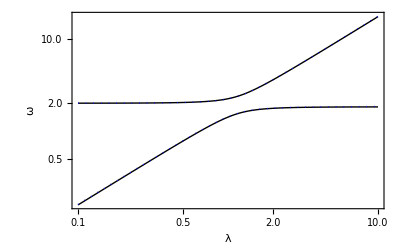

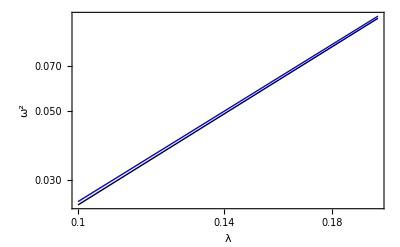

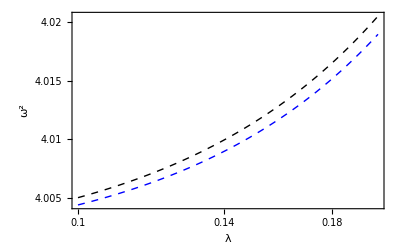

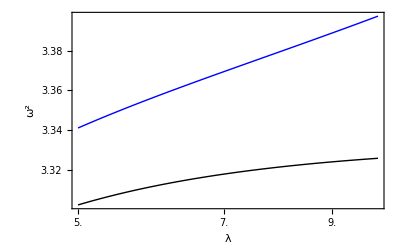

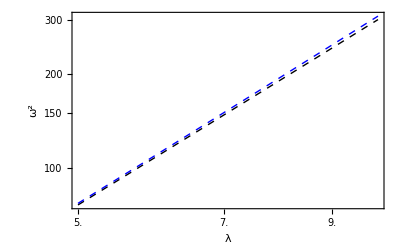

Dropbox/Trabalhos/SingleVortex/shiftG.eps

```mathematica
eqr1=ρ0==(15γ)/(ρ0^3 z0);
eqz1=λ^2 z0==(15γ)/(ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(45γ)/(ρ1^4 z1)+1;
a12[ρ1_,z1_,λ_,γ_]:=(15 γ)/(ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^2 z1^3)+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/SingleVortex/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

### Modulação do Comprimento de espalhamento

{ρ0→4.1849,z0→40.949,α0→0.099159}

{{r[t]→InterpolatingFunction[{{0.,100.}},<>][t],z[t]→InterpolatingFunction[{{0.,100.}},<>][t],α[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

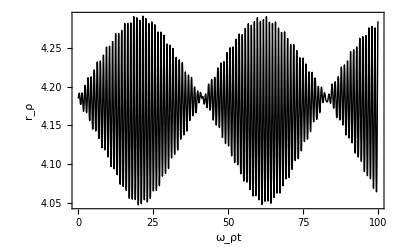

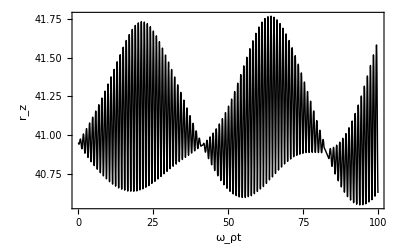

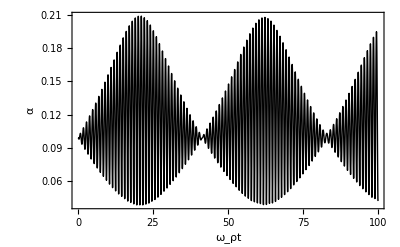

Dropbox/Trabalhos/SingleVortex/l01g800d24o61-r.eps

Dropbox/Trabalhos/SingleVortex/l01g800d24o61-z.eps

Dropbox/Trabalhos/SingleVortex/l01g800d24o61-a.eps

```mathematica
d1[α_]:=(8/315(6-7 α^2 (3+20 α^2+15 α^4)+105 α^4 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d2[α_]:=(8/1575(15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d3[α_]:=(8/945(8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d4[α_]:=(-8/9(4+3 α^2-3 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d5[α_]:=(2/3-α^2+α^4(1+α^2)^(-1/2)(-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)]))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d6[α_]:=(8/10395 (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d7[α_]:=(16/(1575 √(1+α^2))(√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/((8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+D[d5[α],α]


γ[t_]:=γ0+δγ Cos[Ω t]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4γ0 d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2γ0 d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4γ0 D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4d7[a]γ[t])/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2d7[a]γ[t])/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4D[d7[a],a]γ[t])/(r[t]^2 z[t])==0/.a->α[t];
ex=1;
γ0=800;
λ=0.1;
Ω=6.1;
δγ=24;
L=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,100}]


f1=Plot[{Evaluate[r[t]/.se]},{t,0,100},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ρ"},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]
f2=Plot[{Evaluate[z[t]/.se]},{t,0,100},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_z"},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]
f3=Plot[{Evaluate[α[t]/.se]},{t,0,100},Frame->True,Axes->False,FrameLabel->{"ω_ρt","α"},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]

Export["Dropbox/Trabalhos/SingleVortex/l01g800d24o61-r.eps",f1]
Export["Dropbox/Trabalhos/SingleVortex/l01g800d24o61-z.eps",f2]
Export["Dropbox/Trabalhos/SingleVortex/l01g800d24o61-a.eps",f3]

ClearAll[λ,ss,se]

ClearAll[ex,vp,d1,d2,d3,d4,d5,d6,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,ss,se,λ,L,γ,γ0,δγ,eqρ, eqz,eqα,eq1,eq2,eq3,Ω,d7,f1,f2,f3]
```

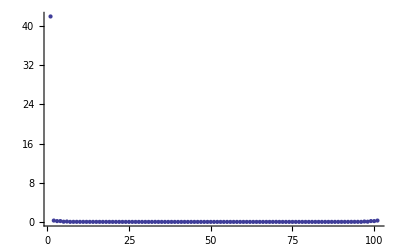

```mathematica
ListPlot[{41.9200087278063,0.2778314922744004,0.16673890835346464,0.1729856379581815,0.04488203125591769,0.08189388339873835,0.012532180212120913,0.019734979504259405,0.01915464288084457,0.016504386942273824,0.01589793729536547,0.014219102857628093,0.013524362577791136,0.012598670796644668,0.01165751718048801,0.011079140662821767,0.010470890545820519,0.009902174007058407,0.00942440594022006,0.008992887399128475,0.008604334680639236,0.008246598829564751,0.007922948211962485,0.0076320595375852845,0.007370285323673538,0.007104039238160782,0.006844260084606551,0.006736885897754226,0.006526225072089214,0.006173756863954748,0.005867092728019023,0.005788546658798335,0.014144293842165796,0.00840652970301442,0.006828423605769865,0.005863160459874526,0.006186458162041225,0.005965822396581081,0.005748860982080089,0.005685441277553079,0.0055977600456131,0.005531197582368369,0.005463938383966304,0.00540981960654131,0.005369528603095359,0.005330993415909508,0.0052995914552666735,0.005276441719447438,0.005258791748424332,0.005247012494414208,0.005241078778494123,0.00524107877849562,0.005247012494411849,0.005258791748424457,0.005276441719446266,0.005299591455270363,0.005330993415906755,0.005369528603096985,0.005409819606538443,0.005463938383969176,0.00553119758236595,0.005597760045612237,0.00568544127755338,0.005748860982076789,0.005965822396582374,0.006186458162040953,0.00586316045987462,0.006828423605771223,0.008406529703013744,0.014144293842162875,0.005788546658796573,0.005867092728018953,0.006173756863955688,0.0065262250720888315,0.006736885897757072,0.006844260084606874,0.007104039238159646,0.0073702853236718635,0.007632059537589166,0.007922948211965748,0.008246598829564187,0.008604334680639442,0.008992887399126133,0.009424405940220417,0.009902174007057922,0.010470890545824828,0.011079140662819136,0.011657517180484711,0.01259867079664608,0.013524362577792036,0.014219102857626651,0.015897937295366288,0.01650438694227459,0.01915464288084473,0.0197349795042598,0.012532180212122988,0.08189388339874067,0.044882031255918005,0.17298563795818397,0.16673890835346253,0.2778314922744001}]
```

### Gráfico dos Modos

```mathematica
Needs["PlotLegends`"]
```

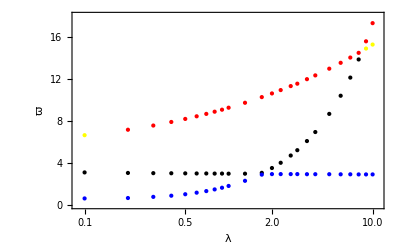

Dropbox/Trabalhos/SingleVortex/modosXlambda.eps

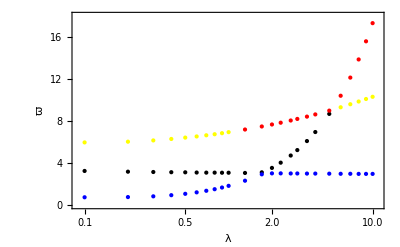

Dropbox/Trabalhos/SingleVortex/modosXlambda2.eps

```mathematica
QM={{0.01,3.31},{0.1,3.10},{0.2,3.05},{0.3,3.03},{0.4,3.02},{0.5,3.01},{0.6,3.00},{0.7,3.00},{0.8,2.99},{0.9,2.99},{1,2.98},{1.3,2.98},{1.7,3.06},{2,3.52},{2.3,4.02},{2.7,4.71},{3,5.22},{3.5,6.09},{4,6.95},{5,8.68},{6,10.41},{7,12.14},{8,13.87}};
BM={{0.01,0.68},{0.1,0.62},{0.2,0.66},{0.3,0.77},{0.4,0.88},{0.5,1.02},{0.6,1.17},{0.7,1.32},{0.8,1.48},{0.9,1.64},{1,1.81},{1.3,2.30},{1.7,2.89},{2,2.94},{2.3,2.94},{2.7,2.94},{3,2.94},{3.5,2.93},{4,2.93},{5,2.93},{6,2.92},{7,2.92},{8,2.91},{9,2.91},{10,2.91}};
QVM={{0.2,7.17},{0.3,7.57},{0.4,7.91},{0.5,8.20},{0.6,8.45},{0.7,8.68},{0.8,8.89},{0.9,9.08},{1,9.27},{1.3,9.74},{1.7,10.28},{2,10.63},{2.3,10.95},{2.7,11.33},{3,11.56},{3.5,11.99},{4,12.35},{5,12.99},{6,13.55},{7,14.05},{8,14.50},{9,15.60},{10,17.33}};
BVM={{0.01,6.43},{0.1,6.65},{9,14.91},{10,15.29}};
f1=ListLogLinearPlot[{QM,BM,QVM,BVM},PlotRange->{{0.09,10.9},{0,18}},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},PlotLegend->{Q,B,QV,BV},LegendSize->{0.2,0.4},LegendShadow->{0,0},PlotStyle->{Black,Blue,Red,Yellow},LegendPosition->{-0.70,0.1}]
Export["Dropbox/Trabalhos/SingleVortex/modosXlambda.eps",f1]
ClearAll[QM,BM,QVM,BVM,f1]

QM={{0.01,3.79},{0.1,3.24},{0.2,3.17},{0.3,3.14},{0.4,3.12},{0.5,3.11},{0.6,3.09},{0.7,3.08},{0.8,3.08},{0.9,3.07},{1,3.07},{1.3,3.05},{1.7,3.11},{2,3.53},{2.3,4.03},{2.7,4.71},{3,5.23},{3.5,6.09},{4,6.95},{5,8.68}};
BM={{0.01,0.83},{0.1,0.73},{0.2,0.75},{0.3,0.82},{0.4,0.93},{0.5,1.06},{0.6,1.2},{0.7,1.35},{0.8,1.5},{0.9,1.66},{1,1.82},{1.3,2.31},{1.7,2.92},{2,3.01},{2.3,3.01},{2.7,3},{3,3},{3.5,2.99},{4,2.99},{5,2.98},{6,2.97},{7,2.97},{8,2.96},{9,2.96},{10,2.96}};
QVM={{1.3,7.19},{1.7,7.48},{2,7.67},{2.3,7.84},{2.7,8.05},{3,8.20},{3.5,8.42},{4,8.63},{5,8.99},{6,10.41},{7,12.14},{8,13.87},{9,15.6},{10,17.33}};
BVM={{0.01,6.9},{0.1,5.96},{0.2,6.03},{0.3,6.15},{0.4,6.29},{0.5,6.42},{0.6,6.53},{0.7,6.64},{0.8,6.74},{0.9,6.84},{1,6.94},{6,9.31},{7,9.6},{8,9.86},{9,10.10},{10,10.31}};
f2=ListLogLinearPlot[{QM,BM,QVM,BVM},PlotRange->{{0.09,10.9},{0,18}},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},PlotLegend->{Q,B,QV,BV},LegendSize->{0.2,0.4},LegendShadow->{0,0},PlotStyle->{Black,Blue,Red,Yellow},LegendPosition->{-0.70,0.1}]
Export["Dropbox/Trabalhos/SingleVortex/modosXlambda2.eps",f2]
ClearAll[QM,BM,QVM,BVM,f2]
```

### Estabilidade de Vortices

## Expansão livre

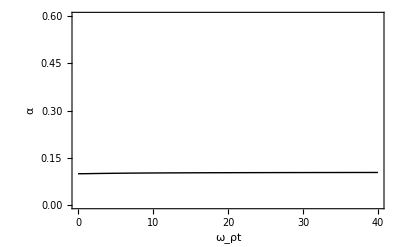

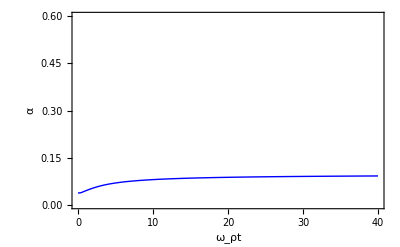

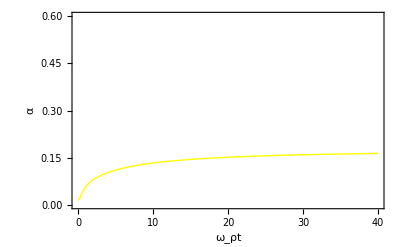

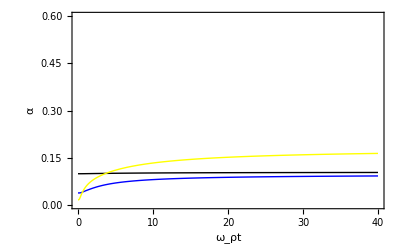

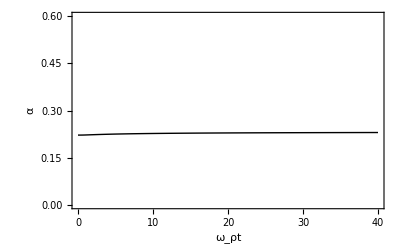

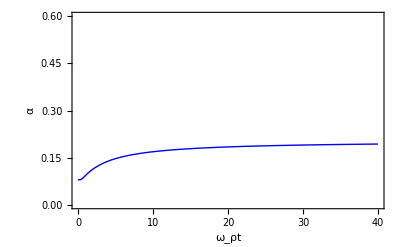

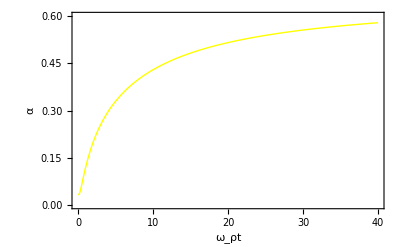

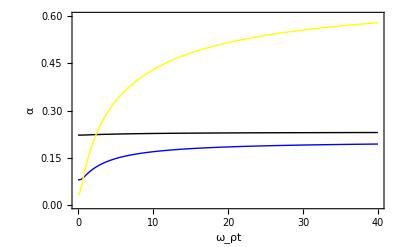

Dropbox/Trabalhos/SingleVortex/vel-r.eps

Dropbox/Trabalhos/SingleVortex/vel-r2.eps

```mathematica
d1[α_]:=(8/315(6-7 α^2 (3+20 α^2+15 α^4)+105 α^4 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d2[α_]:=(8/1575(15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d3[α_]:=(8/945(8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d4[α_]:=(-8/9(4+3 α^2-3 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d5[α_]:=(2/3-α^2+α^4(1+α^2)^(-1/2)(-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)]))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d6[α_]:=(8/10395 (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d7[α_]:=(16/(1575 √(1+α^2))(√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/((8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+D[d5[α],α]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4γ D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4d7[a]γ)/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2d7[a]γ)/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4D[d7[a],a]γ)/(r[t]^2 z[t])==0/.a->α[t];

γ=800;
L=1;
ex=0;

ClearAll[λ,ss,se]

λ=0.1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f1=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt",α},PlotRange->{0,0.6},RotateLabel->False,PlotStyle->{Black}]


ClearAll[λ,ss,se]

λ=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f2=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt",α},PlotRange->{0,0.6},RotateLabel->False,PlotStyle->{Blue}]


ClearAll[λ,ss,se]

λ=8;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];


f3=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt",α},PlotRange->{0,0.6},RotateLabel->False,PlotStyle->{Yellow}]

g1=Show[f1,f2,f3]

ClearAll[λ,L,γ]

γ=800;
L=2;
ex=0;

ClearAll[λ,ss,se]

λ=0.1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f4=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt",α},PlotRange->{0,0.6},RotateLabel->False,PlotStyle->{Black}]


ClearAll[λ,ss,se]

λ=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f5=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt",α},PlotRange->{0,0.6},RotateLabel->False,PlotStyle->{Blue}]


ClearAll[λ,ss,se]

λ=8;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];


f6=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt",α},PlotRange->{0,0.6},RotateLabel->False,PlotStyle->{Yellow}]

g2=Show[f4,f5,f6]

Export["Dropbox/Trabalhos/SingleVortex/vel-r.eps",g1]

Export["Dropbox/Trabalhos/SingleVortex/vel-r2.eps",g2]

ClearAll[d1,d2,d3,d4,d5,d6,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,eq1,eq2,eq3,eqρ,eqz,eqα,λ,γ,se,ss,L,ex,vp,f1,f2,f3,g1,d7,g2,f4,f5,f6]
```

#### Comparação com a simulação númerica.

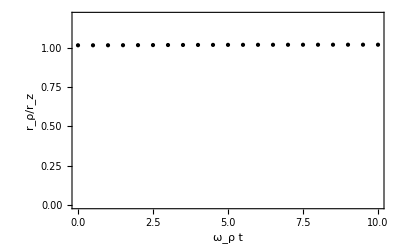

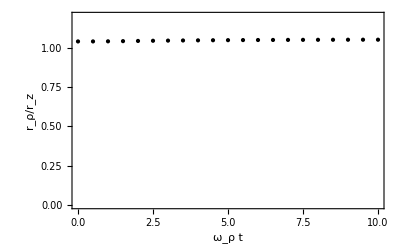

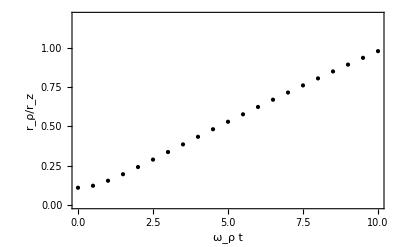

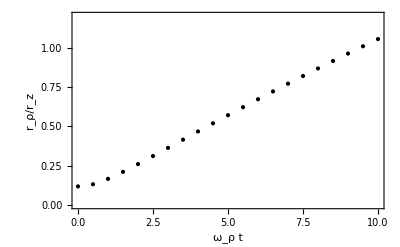

{ρ0→4.1849,z0→40.949,α0→0.099159}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

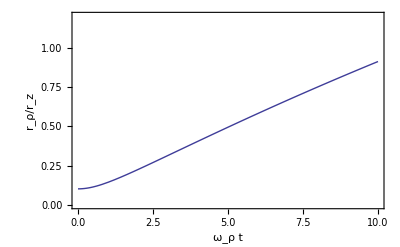

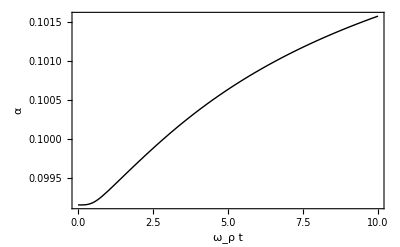

{ρ0→4.26523,z0→40.739,α0→0.221961}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

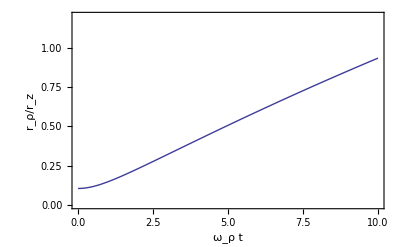

{ρ0→6.55743,z0→6.53227,α0→0.0381328}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

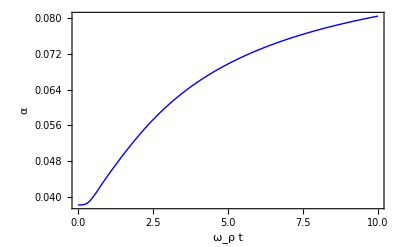

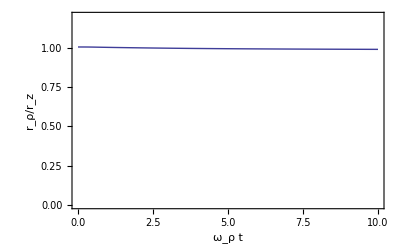

{ρ0→6.58172,z0→6.51942,α0→0.0800259}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

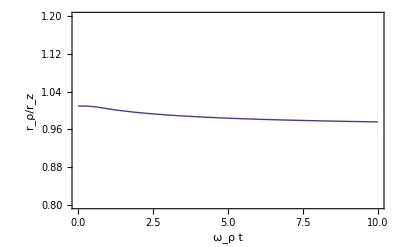

{ρ0→9.92963,z0→1.23846,α0→0.033207}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

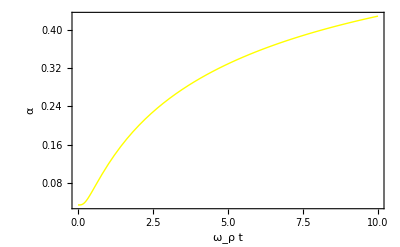

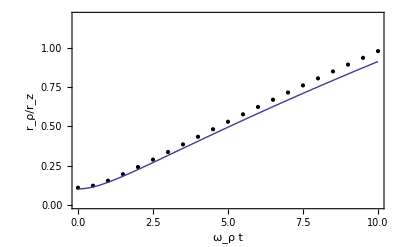

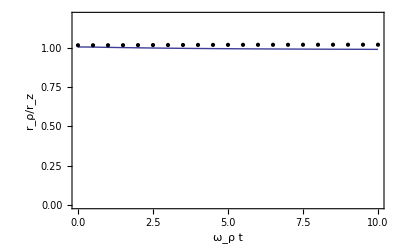

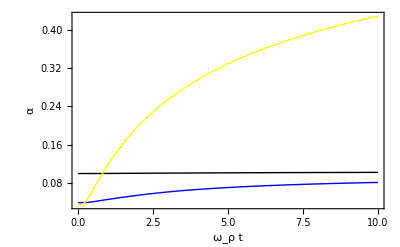

Dropbox/Trabalhos/SingleVortex/nume01.eps

Dropbox/Trabalhos/SingleVortex/nume1.eps

Dropbox/Trabalhos/SingleVortex/vel-w.eps

```mathematica
d1[α_]:=(8/315(6-7 α^2 (3+20 α^2+15 α^4)+105 α^4 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d2[α_]:=(8/1575(15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d3[α_]:=(8/945(8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d4[α_]:=(-8/9(4+3 α^2-3 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d5[α_]:=(2/3-α^2+α^4(1+α^2)^(-1/2)(-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)]))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d6[α_]:=(8/10395 (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/(8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))
d7[α_]:=(16/(1575 √(1+α^2))(√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))/((8/45(3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) (-1/4 Log[((1-√(1+α^2))^2)/((1+√(1+α^2))^2)])))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+D[d5[α],α]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4γ D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4d7[a]γ)/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2d7[a]γ)/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4D[d7[a],a]γ)/(r[t]^2 z[t])==0/.a->α[t];

n11=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/SingleVortex/R-l1-lam00.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/SingleVortex/Z-l1-lam00.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},PlotRange->{0,1.2},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},RotateLabel->False]

n21=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/SingleVortex/R-l2-lam00.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/SingleVortex/Z-l2-lam00.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},PlotRange->{0,1.2},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},RotateLabel->False]

n101=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/SingleVortex/R-l1-lam01.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/SingleVortex/Z-l1-lam01.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.0,1.2},RotateLabel->False]

n201=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/SingleVortex/R-l2-lam01.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/SingleVortex/Z-l2-lam01.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.0,1.2},RotateLabel->False]

λ=0.1;
γ=800;
L=1;
ex=0;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]


fe101=Plot[Evaluate[r[t]/.se]/Evaluate[z[t]/.se],{t,0,10},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.0,1.2},RotateLabel->False]
fα01=Plot[Evaluate[α[t]/.se],{t,0,10},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",α},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]

ClearAll[ss,se,L]

L=2;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]

fe201=Plot[Evaluate[r[t]/.se]/Evaluate[z[t]/.se],{t,0,10},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.0,1.2},RotateLabel->False]

ClearAll[ss,se,λ,L]
λ=1;
L=1;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]

fα1=Plot[Evaluate[α[t]/.se],{t,0,10},Frame->True,RotateLabel->False,Axes->False,FrameLabel->{"ω_ρ t",α},PlotRange->All,PlotStyle->{Blue}]

fe11=Plot[Evaluate[r[t]/.se]/Evaluate[z[t]/.se],{t,0,10},Frame->True,RotateLabel->False,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.0,1.2}]

ClearAll[ss,se,L]

L=2;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]

fe21=Plot[Evaluate[r[t]/.se]/Evaluate[z[t]/.se],{t,0,10},Frame->True,RotateLabel->False,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.8,1.2}]

ClearAll[ss,se,λ]
λ=8;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]

fα10=Plot[Evaluate[α[t]/.se],{t,0,10},Frame->True,RotateLabel->False,Axes->False,FrameLabel->{"ω_ρ t",α},PlotRange->All,PlotStyle->{Yellow}]

g1=Show[n101,fe101]
g2=Show[n11,fe11]
g3=Show[fα01,fα1,fα10]

Export["Dropbox/Trabalhos/SingleVortex/nume01.eps",g1]
Export["Dropbox/Trabalhos/SingleVortex/nume1.eps",g2]
Export["Dropbox/Trabalhos/SingleVortex/vel-w.eps",g3]

ClearAll[d1,d2,d3,d4,d5,d6,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,eq1,eq2,eq3,eqρ,eqz,eqα,λ,γ,se,ss,L,ex,fe101,fe11,fe21,fe201,n11,n101,g1,g2,g3,fα01,fα1,fα10,n21,n201]
```